```mathematica
Basedir="/Users/yifan/Library/CloudStorage/Dropbox/Current Projects/2023-AlonLab-sickspans/NIA figure/";
C2004=Import[Basedir<>"Lifespan_C2004.xlsx"][[1]];
C2005=Import[Basedir<>"Lifespan_C2005.xlsx"][[1]];
C2006=Import[Basedir<>"Lifespan_C2006.xlsx"][[1]];
C2007=Import[Basedir<>"Lifespan_C2007.xlsx"][[1]];
C2009=Import[Basedir<>"Lifespan_C2009.xlsx"][[1]];
C2010=Import[Basedir<>"Lifespan_C2010.xlsx"][[1]];
C2011=Import[Basedir<>"Lifespan_C2011.xlsx"][[1]];
C2012=Import[Basedir<>"Lifespan_C2012.xlsx"][[1]];
C2013=Import[Basedir<>"Lifespan_C2013.xlsx"][[1]];
C2014=Import[Basedir<>"Lifespan_C2014.xlsx"][[1,;;,;;11]];
C2015=Import[Basedir<>"Lifespan_C2015.xlsx"][[1]];
C2016=Import[Basedir<>"Lifespan_C2016.xlsx"][[1]];
C2017=Import[Basedir<>"Lifespan_C2017.xlsx"][[1]]/."CAPT"->"Capt";
```

```mathematica
meanAround[x_]:=Around[Mean@#,(StandardDeviation@#)/(√(Length@#))]&/@(xᵀ)
```

```mathematica
TrimmedMeanpaclet:ref/TrimmedMean[list,{Subscript[f, 1],Subscript[f, 2]}]
```

```mathematica
BetterSmoothDensityHistogram[data_,cs_List,opt___]:=Module[{d,domain,p,q,c},
d=SmoothKernelDistribution[data];
domain=MinMax/@(dataᵀ);
p=PDF[d,data];
c=Quantile[p,1-cs];
ContourPlot[PDF[d,{x,y}],{x,Sequence@@domain[[1]]},{y,Sequence@@domain[[2]]},Contours->c,opt]]
```

```mathematica
Jdata=(Join@@(DeleteCases[(Join@@ParallelTable[
Table[(Print[{set[[2,2]],q}];
Table[
Module[{data=Cases[set,{__,g,_,#,__,_,y_,x_}:>{x,1-Round@y}]&/@{"Control",q}},
If[data[[2]]=={},{},
{
(
(TrimmedMean[#,{.1,0.}]/{365,Sqrt@TrimmedVariance[#,{.1,0.}]}&@SurvivalDistribution[EventData@@(#ᵀ),Method->"KaplanMeier"])&/@RandomChoice[#,{200,Length@#}])&/@data,
{set[[2,2]],q,g}}]
],
{g,{"m","f"}}]),
{q,DeleteCases[Union[set[[2;;,6]]],"Control"]}],
{set,(ToExpression["C20"<>#]&/@{"04","05","06","07","09","10","11","12","13","14","15","16","17"})}])ᵀ,{},{2}]));
```

{C2004,4-OH-PBN}

{C2006,Rapa}

{C2007,Cur}

{C2009,17aE2}

{C2010,FO_hi}

{C2011,17aE2_hi}

{C2012,ACA}

{C2013,ACA_hi}

{C2014,Asp_200}

{C2015,bGPA}

{C2016,17aE2_16m}

{C2017,BD}

{C2016,17aE2_20m}

{C2006,Res_hi}

{C2011,Met}

{C2015,DMAG}

{C2012,HBX}

{C2014,Asp_60}

{C2007,GTE}

{C2017,Capt}

{C2009,ACA}

{C2013,ACA_lo}

{C2016,Cana}

{C2010,FO_lo}

{C2004,Asp}

{C2017,Leu}

{C2014,Gly}

{C2015,Min}

{C2010,NDGA_hi}

{C2007,MCTO}

{C2006,Res_lo}

{C2009,MB}

{C2012,INT-767}

{C2013,ACA_mid}

{C2016,CC}

{C2011,MetRapa}

{C2004,NDGA}

{C2017,PB125}

{C2015,MitoQ}

{C2014,Inu}

{C2007,OAA}

{C2009,Rapa_hi}

{C2006,Sim_hi}

{C2010,NDGA_lo}

{C2013,UA}

{C2011,Prot}

{C2016,GGA}

{C2004,NFP}

{C2010,NDGA_mid}

{C2017,RaAc16}

{C2015,Rapa_hi_continuous}

{C2009,Rapa_lo}

{C2014,TM5441}

{C2007,Res}

{C2006,Sim_lo}

{C2011,UDCA}

{C2016,MIF098}

{C2005,CAPE_hi}

{C2017,RaAc9}

{C2009,Rapa_mid}

{C2015,Rapa_hi_cycle}

{C2016,NR}

{C2005,CAPE_lo}

{C2017,Sul}

{C2015,Rapa_hi_start_stop}

{C2005,Enal}

{C2017,Syr}

{C2005,Rapa}

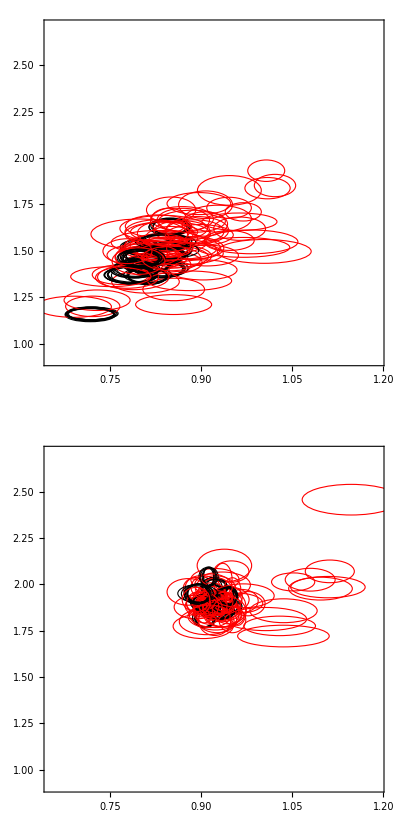

```mathematica
GraphicsGrid@({#}&/@(Graphics[#,AspectRatio->1,ImageSize->Large,Frame->True,PlotRange->{Log@({700,1200}/365),Log@{2.5,15}},(*FrameLabel->{"Longevity (years)","Steepness"},*)FrameStyle->Directive[Black,14],Axes->True,AxesOrigin->Mean@#[[;;,3,1]]]&/@((GatherBy[Jdata,#[[2,3]]&]/.x:{{{{_Real,_Real}..},{{_Real,_Real}..}},_}:>{
FaceForm[],EdgeForm[Black],Ellipsoid@@(VectorAround[Mean@Log@x[[1,1]],Covariance@Log@x[[1,1]]]),
EdgeForm[Red],Tooltip[Ellipsoid@@(VectorAround[Mean@Log@x[[1,2]],Covariance@Log@x[[1,2]]]),x[[2]]]}))))
```

```mathematica
MultiNormalDistDifferenceTest[{data1_,data2_}]:=Dot[Inverse@Transpose@CholeskyDecomposition[Covariance@data1+Covariance@data2],Mean@data1-Mean@data2]
(*MultiNormalDistDifferenceTestPValue[{data1_,data2_}]:=N[SurvivalFunction[ChiSquareDistribution[Length@data1],Total[(#^2&)/@MultiNormalDistDifferenceTest[{data1,data2}]]]]*)
MultiNormalDistDifferenceTestPValue[{data1_,data2_}]:=(
zvalues=MultiNormalDistDifferenceTest[{data1,data2}];
N[SurvivalFunction[ChiSquareDistribution[Length@zvalues],Total[(#^2&)/@zvalues]]])
NormalDistDifferenceTest[{data1_,data2_}]:=(Mean@data1-Mean@data2)/Sqrt[Variance@data1+Covariance@data2]
HostellingTsquared[{data1_,data2_}]:=Dot[Mean@data1-Mean@data2,Dot[Inverse[Covariance@data1+Covariance@data2],Mean@data1-Mean@data2]]
HostellingTsquaredTestPValue[{data1_,data2_}]:=(
tsquared=HostellingTsquared[{data1,data2}];
N[SurvivalFunction[HotellingTSquareDistribution[2,198],tsquared]])
```

```mathematica
NMTestZs=Join@@Map[{MultiNormalDistDifferenceTest@Log@#[[1,;;,;;,;;]],#[[2]]}&,GatherBy[Jdata,#[[2,3]]&],{2}];
SteepnessNMTestZs=Join@@Map[{NormalDistDifferenceTest@Log@#[[1,;;,;;,2]],#[[2]]}&,GatherBy[Jdata,#[[2,3]]&],{2}];
HostellingTsquares=Join@@Map[{HostellingTsquared@Log@#[[1,;;,;;,;;]],#[[2]]}&,GatherBy[Jdata,#[[2,3]]&],{2}];
```

```mathematica
relative=DeleteCases[(Join@@ParallelTable[
Table[(Print[set[[2,2]],q];
Table[
Module[{data=Cases[set,{__,g,_,#,__,_,y_,x_}:>{x,1-Round@y}]&/@{"Control",q}},
If[data[[2]]=={},{},
{
meanAround[Log@((#[[2]])/(#[[1]]))&/@Transpose@(
(TrimmedMean[#,{.1,0.}]/{1,Sqrt@TrimmedVariance[#,{.1,0.}]}&@SurvivalDistribution[EventData@@(#ᵀ),Method->"KaplanMeier"])&/@RandomChoice[#,{100,Length@#}]&/@data)],
{q,g,set[[2,2]]}}]
],
{g,{"m","f"}}]),
{q,DeleteCases[Union[set[[2;;,6]]],"Control"]}],
{set,(ToExpression["C20"<>#]&/@{"04","05","06","07","09","10","11","12","13","14","15","16","17"})}])ᵀ,{},{2}];
```

C20044-OH-PBN

C2006Rapa

C200917aE2

C201117aE2_hi

C2009ACA

C2006Res_hi

C2011Met

C2004Asp

C2009MB

C2006Res_lo

C2011MetRapa

C2004NDGA

C2009Rapa_hi

C2006Sim_hi

C2011Prot

C2004NFP

C2009Rapa_lo

C2006Sim_lo

C2011UDCA

C2005CAPE_hi

C2009Rapa_mid

C2007Cur

C2012ACA

C2005CAPE_lo

C2010FO_hi

C2007GTE

C2012HBX

C2005Enal

C2010FO_lo

C2007MCTO

C2012INT-767

C2005Rapa

C2010NDGA_hi

C2007OAA

C2013ACA_hi

C2015bGPA

C2007Res

C2010NDGA_lo

C2013ACA_lo

C2015DMAG

C2010NDGA_mid

C201617aE2_16m

C2017BD

C2013ACA_mid

C2015Min

C201617aE2_20m

C2016Cana

C2017Capt

C2013UA

C2015MitoQ

C2016CC

C2017Leu

C2015Rapa_hi_continuous

C2014Asp_200

C2016GGA

C2017PB125

C2015Rapa_hi_cycle

C2014Asp_60

C2016MIF098

C2017RaAc16

C2015Rapa_hi_start_stop

C2014Gly

C2016NR

C20044-OH-PBN

C2006Rapa

C2007Cur

C200917aE2

C2010FO_hi

C201117aE2_hi

C2012ACA

C2013ACA_hi

C2014Asp_200

C2015bGPA

C201617aE2_16m

C2017BD

C201617aE2_20m

C2013ACA_lo

C2007GTE

C2011Met

C2012HBX

C2015DMAG

C2009ACA

C2014Asp_60

C2006Res_hi

C2010FO_lo

C2016Cana

C2004Asp

C2017Capt

C2007MCTO

C2009MB

C2012INT-767

C2011MetRapa

C2014Gly

C2015Min

C2016CC

C2013ACA_mid

C2010NDGA_hi

C2006Res_lo

C2017Leu

C2004NDGA

C2007OAA

C2011Prot

C2014Inu

C2009Rapa_hi

C2015MitoQ

C2016GGA

C2013UA

C2010NDGA_lo

C2006Sim_hi

C2004NFP

C2017PB125

C2010NDGA_mid

C2011UDCA

C2014TM5441

C2007Res

C2015Rapa_hi_continuous

C2016MIF098

C2009Rapa_lo

C2006Sim_lo

C2005CAPE_hi

C2017RaAc16

C2015Rapa_hi_cycle

C2016NR

C2009Rapa_mid

C2017RaAc9

C2005CAPE_lo

C2015Rapa_hi_start_stop

C2017Sul

C2005Enal

C2017Syr

C2005Rapa

C20044-OH-PBN

C2006Rapa

C2007Cur

C200917aE2

C2010FO_hi

C201117aE2_hi

C2012ACA

C2013ACA_hi

C2014Asp_200

C2015bGPA

C201617aE2_16m

C2017BD

C201617aE2_20m

C2011Met

C2007GTE

C2012HBX

C2014Asp_60

C2013ACA_lo

C2006Res_hi

C2009ACA

C2004Asp

C2017Capt

C2010FO_lo

C2015DMAG

C2016Cana

C2015Min

C2011MetRapa

C2012INT-767

C2009MB

C2014Gly

C2013ACA_mid

C2006Res_lo

C2010NDGA_hi

C2016CC

C2017Leu

C2004NDGA

C2007MCTO

C2015MitoQ

C2009Rapa_hi

C2011Prot

C2013UA

C2014Inu

C2006Sim_hi

C2010NDGA_lo

C2017PB125

C2016GGA

C2004NFP

C2007OAA

C2010NDGA_mid

C2015Rapa_hi_continuous

C2009Rapa_lo

C2011UDCA

C2014TM5441

C2006Sim_lo

C2016MIF098

C2017RaAc16

C2005CAPE_hi

C2007Res

C2015Rapa_hi_cycle

C2009Rapa_mid

C2016NR

C2017RaAc9

C2005CAPE_lo

C2015Rapa_hi_start_stop

C2017Sul

C2005Enal

C2017Syr

C2005Rapa

C20044-OH-PBN

C2006Rapa

C2007Cur

C200917aE2

C2010FO_hi

C201117aE2_hi

C2012ACA

C2013ACA_hi

C2014Asp_200

C2015bGPA

C201617aE2_16m

C2017BD

C201617aE2_20m

C2010FO_lo

C2012HBX

C2007GTE

C2009ACA

C2006Res_hi

C2011Met

C2014Asp_60

C2017Capt

C2004Asp

C2015DMAG

C2013ACA_lo

C2016Cana

C2010NDGA_hi

C2006Res_lo

C2007MCTO

C2014Gly

C2017Leu

C2011MetRapa

C2012INT-767

C2013ACA_mid

C2009MB

C2015Min

C2016CC

C2004NDGA

C2016GGA

C2007OAA

C2010NDGA_lo

C2006Sim_hi

C2011Prot

C2013UA

C2014Inu

C2015MitoQ

C2017PB125

C2009Rapa_hi

C2004NFP

C2010NDGA_mid

C2016MIF098

C2007Res

C2006Sim_lo

C2014TM5441

C2009Rapa_lo

C2011UDCA

C2015Rapa_hi_continuous

C2017RaAc16

C2005CAPE_hi

C2016NR

C2009Rapa_mid

C2015Rapa_hi_cycle

C2017RaAc9

C2005CAPE_lo

C2015Rapa_hi_start_stop

C2017Sul

C2005Enal

C2017Syr

C2005Rapa

C20044-OH-PBN

C2006Rapa

C2007Cur

C200917aE2

C2010FO_hi

C201117aE2_hi

C2012ACA

C2013ACA_hi

C2014Asp_200

C2015bGPA

C201617aE2_16m

C2017BD

C201617aE2_20m

C2006Res_hi

C2012HBX

C2007GTE

C2004Asp

C2010FO_lo

C2011Met

C2009ACA

C2013ACA_lo

C2016Cana

C2014Asp_60

C2015DMAG

C2017Capt

C2009MB

C2006Res_lo

C2007MCTO

C2011MetRapa

C2012INT-767

C2010NDGA_hi

C2017Leu

C2013ACA_mid

C2016CC

C2004NDGA

C2014Gly

C2015Min

C2007OAA

C2009Rapa_hi

C2006Sim_hi

C2011Prot

C2004NFP

C2017PB125

C2013UA

C2010NDGA_lo

C2014Inu

C2015MitoQ

C2016GGA

C2010NDGA_mid

C2007Res

C2009Rapa_lo

C2006Sim_lo

C2011UDCA

C2014TM5441

C2005CAPE_hi

C2017RaAc16

C2015Rapa_hi_continuous

C2016MIF098

C2009Rapa_mid

C2005CAPE_lo

C2016NR

C2015Rapa_hi_cycle

C2017RaAc9

C2015Rapa_hi_start_stop

C2005Enal

C2017Sul

C2017Syr

C2005Rapa

C2017RaAc9

C2014Inu

C2017Sul

C2014TM5441

C2017Syr

```mathematica
steepnessMWTestRes=Map[{{1,0}+MannWhitneyTest[#,Automatic,"TestData"]/{-1/2 Times@@(Length/@#),1/132}&@#[[1,;;,;;,2]],#[[2]]}&,GatherBy[Jdata,#[[2,3]]&],{2}];
```

```mathematica
(*seg={#[[2]],#[[3]],#[[1]]}&/@Join@@(Select[SortBy[#,#[[1,1]]&],Abs@#[[1,1]]>.9&&#[[1,2]]<0.05&][[;;,2]]&/@steepnessMWTestRes)*)
```

```mathematica
sortedHTSPvalues={N[SurvivalFunction[HotellingTSquareDistribution[2,198],#[[1]]]],#[[2]]}&/@ReverseSortBy[HostellingTsquares,#[[1]]&];
HTSsig=Append[#[[2,2;;]],#[[2,1]]]&/@sortedHTSPvalues[[;;Pick[Range[Length@sortedHTSPvalues],Table[sortedHTSPvalues[[i,1]]<=0.05*i/Length@sortedHTSPvalues,{i,Length@sortedHTSPvalues}]][[-1]]]]
```

{{Rapa_hi,f,C2009},{RaAc9,f,C2017},{Rapa_mid,f,C2009},{MetRapa,f,C2011},{RaAc9,m,C2017},{Rapa,f,C2006},{RaAc16,f,C2017},{Rapa,f,C2005},{ACA,m,C2009},{Rapa_lo,f,C2009},{MetRapa,m,C2011},{ACA_hi,m,C2013},{Rapa_hi_continuous,f,C2015},{ACA_mid,m,C2013},{Rapa,m,C2005},{17aE2_hi,m,C2011},{17aE2_16m,m,C2016},{Rapa_hi,m,C2009},{Cana,m,C2016},{Rapa,m,C2006},{ACA_lo,m,C2013},{Rapa_hi_cycle,f,C2015},{RaAc16,m,C2017},{Rapa_hi_cycle,m,C2015},{NDGA,m,C2004},{NDGA_mid,m,C2010},{Capt,m,C2017},{ACA,m,C2012},{NDGA_hi,m,C2010},{17aE2,m,C2009},{Rapa_hi_continuous,m,C2015},{17aE2_20m,m,C2016},{Capt,f,C2017},{BD,m,C2017},{ACA_mid,f,C2013},{ACA_hi,f,C2013},{Asp,m,C2004},{ACA,f,C2009}}

```mathematica
sortedPvalues={N[SurvivalFunction[ChiSquareDistribution[2],Total[(#^2&)/@#[[1]]]]],#[[2]]}&/@ReverseSortBy[NMTestZs,Total[(#^2&)/@#[[1]]]&];
sig=Append[#[[2,2;;]],#[[2,1]]]&/@sortedPvalues[[;;Pick[Range[Length@sortedPvalues],Table[sortedPvalues[[i,1]]<=0.05*i/Length@sortedPvalues,{i,Length@sortedPvalues}]][[-1]]]]
(*one sideded test alpha=0.05*)
```

{{Rapa_hi,f,C2009},{RaAc9,f,C2017},{Rapa_mid,f,C2009},{MetRapa,f,C2011},{RaAc9,m,C2017},{Rapa,f,C2006},{RaAc16,f,C2017},{Rapa,f,C2005},{ACA,m,C2009},{Rapa_lo,f,C2009},{MetRapa,m,C2011},{ACA_hi,m,C2013},{Rapa_hi_continuous,f,C2015},{ACA_mid,m,C2013},{Rapa,m,C2005},{17aE2_hi,m,C2011},{17aE2_16m,m,C2016},{Rapa_hi,m,C2009},{Cana,m,C2016},{Rapa,m,C2006},{ACA_lo,m,C2013},{Rapa_hi_cycle,f,C2015},{RaAc16,m,C2017},{Rapa_hi_cycle,m,C2015},{NDGA,m,C2004},{NDGA_mid,m,C2010},{Capt,m,C2017},{ACA,m,C2012},{NDGA_hi,m,C2010},{17aE2,m,C2009},{Rapa_hi_continuous,m,C2015},{17aE2_20m,m,C2016},{Capt,f,C2017},{BD,m,C2017},{ACA_mid,f,C2013},{ACA_hi,f,C2013},{Asp,m,C2004},{ACA,f,C2009},{Rapa_mid,m,C2009}}

```mathematica
LSespval=Join@@ParallelTable[
Table[(Print[set[[2,2]],q];
Table[
Module[{data=Cases[set,{__,g,_,#,__,_,y_,x_}:>{x,1-Round@y}]&/@{"Control",q}},
If[data[[2]]=={},{},
{
{Exp[#[[2]]-#[[1]]]&@(meanAround/@Log@#),MultiNormalDistDifferenceTest@Log@#,MultiNormalDistDifferenceTestPValue@Log@#}&@(((TrimmedMean[#,{.1,0.}]/{365,Sqrt@TrimmedVariance[#,{.1,0.}]}&@SurvivalDistribution[EventData@@(#ᵀ),Method->"KaplanMeier"])&/@RandomChoice[#,{100,Length@#}])&/@data),
q(*{q,g}*)}]
],
{g,{"m","f"}}]),
{q,DeleteCases[Union[set[[2;;,6]]],"Control"]}],
{set,(ToExpression["C20"<>#]&/@{"04","05","06","07","09","10","11","12","13","14","15","16","17"}) }];
```

C20044-OH-PBN

C2006Rapa

C2007Cur

C200917aE2

C2010FO_hi

C201117aE2_hi

C2012ACA

C2013ACA_hi

C2014Asp_200

C2015bGPA

C201617aE2_16m

C2017BD

C201617aE2_20m

C2007GTE

C2009ACA

C2014Asp_60

C2013ACA_lo

C2017Capt

C2012HBX

C2006Res_hi

C2004Asp

C2010FO_lo

C2011Met

C2015DMAG

C2016Cana

C2007MCTO

C2013ACA_mid

C2009MB

C2014Gly

C2017Leu

C2012INT-767

C2011MetRapa

C2010NDGA_hi

C2015Min

C2016CC

C2004NDGA

C2006Res_lo

C2007OAA

C2011Prot

C2013UA

C2014Inu

C2009Rapa_hi

C2017PB125

C2015MitoQ

C2016GGA

C2010NDGA_lo

C2006Sim_hi

C2004NFP

C2010NDGA_mid

C2007Res

C2011UDCA

C2009Rapa_lo

C2014TM5441

C2015Rapa_hi_continuous

C2017RaAc16

C2016MIF098

C2006Sim_lo

C2005CAPE_hi

C2009Rapa_mid

C2017RaAc9

C2016NR

C2015Rapa_hi_cycle

C2005CAPE_lo

C2017Sul

C2015Rapa_hi_start_stop

C2005Enal

C2017Syr

C2005Rapa

```mathematica
volcanoPlots=Table[ListPlot[Join[
Table[
Callout[{Log@#[[1,1,j,1]],#[[1,3]]},#[[2]]]&/@Cases[(DeleteCases[#,{},∞]&/@Transpose@LSespval)[[i]],({_,Alternatives@@#}&/@Map[First,Reverse@GatherBy[sig,#[[2]]&],{2}])[[i]]]
,{i,2}],
Table[
{Log@#[[1,1,j,1]],#[[1,3]]}&/@Cases[(DeleteCases[#,{},∞]&/@Transpose@LSespval)[[i]],({_,Except[Alternatives@@#]}&/@Map[First,Reverse@GatherBy[sig,#[[2]]&],{2}])[[i]]]
,{i,2}]
],
PlotRange->{All,All},Frame->True,
ScalingFunctions->{None,{-Log@#&,Exp[-#]&}},
FrameLabel->{Style[(("Ln(Relative "<>#)&/@{"Longevity)","Steepness)"})[[j]],14],Style["p-value", 16]},
FrameStyle->Directive[12,Black],
PlotMarkers->(Style[#[[1]],#[[2]],20]&/@{{♂,Darker@Green},{♀,Orange},{♂,Lighter[Green,0.6]},{♀,Lighter[Orange,0.65]}})
],{j,2}];
```

```mathematica
GraphicsGrid[{volcanoPlots},
ImageSize->1200]
```

-Graphics-

```mathematica
sig=HTSsig
```

{{Rapa_hi,f,C2009},{RaAc9,f,C2017},{Rapa_mid,f,C2009},{MetRapa,f,C2011},{RaAc9,m,C2017},{Rapa,f,C2006},{RaAc16,f,C2017},{Rapa,f,C2005},{ACA,m,C2009},{Rapa_lo,f,C2009},{MetRapa,m,C2011},{ACA_hi,m,C2013},{Rapa_hi_continuous,f,C2015},{ACA_mid,m,C2013},{Rapa,m,C2005},{17aE2_hi,m,C2011},{17aE2_16m,m,C2016},{Rapa_hi,m,C2009},{Cana,m,C2016},{Rapa,m,C2006},{ACA_lo,m,C2013},{Rapa_hi_cycle,f,C2015},{RaAc16,m,C2017},{Rapa_hi_cycle,m,C2015},{NDGA,m,C2004},{NDGA_mid,m,C2010},{Capt,m,C2017},{ACA,m,C2012},{NDGA_hi,m,C2010},{17aE2,m,C2009},{Rapa_hi_continuous,m,C2015},{17aE2_20m,m,C2016},{Capt,f,C2017},{BD,m,C2017},{ACA_mid,f,C2013},{ACA_hi,f,C2013},{Asp,m,C2004},{ACA,f,C2009}}

```mathematica
BHFdrThreshold[pvalues_,alpha_:0.05]:=Pick[Sort@pvalues, Table[Sort[pvalues][[i]]<=alpha*i/Length@pvalues,{i,Length@pvalues}] ][[-1]];
BHFdrThreshold[First/@sortedHTSPvalues,0.05]
```

0.0125125

```mathematica
(*SteepSortedPvalues={1.-CDF[NormalDistribution[0,1],Abs@#[[1]]],#[[2]]}&/@ReverseSortBy[SteepnessNMTestZs,Abs@#[[1]]&];
Steep=Append[#[[2,2;;]],#[[2,1]]]&/@Pick[SteepSortedPvalues,Table[SteepSortedPvalues[[i,1]]<=0.075*i/Length@SteepSortedPvalues,{i,Length@SteepSortedPvalues}]](*two sideded test alpha=0.15*)*)
```

```mathematica
nonScaling=#[[2]]&/@SortBy[Select[{{#[[7]],#[[6]]},{#[[3]],#[[2]],#[[4]]}}&/@Import[Basedir<>"AFT+KS test results.csv"][[2;;]],#[[1,2]]!=">= 0.8"&& #[[1,2]]<0.1&],#[[1,2]]&]
```

{{Rapa_hi,f,C2009},{ACA_hi,m,C2013},{GTE,f,C2007},{ACA,m,C2009},{NDGA_mid,m,C2010},{17aE2_16m,m,C2016},{RaAc9,m,C2017},{ACA_mid,m,C2013},{NDGA_hi,m,C2010},{Capt,m,C2017},{Rapa_hi_continuous,f,C2015},{17aE2,m,C2009},{BD,m,C2017}}

```mathematica
categories={
{"ATTAC+AP", "D+Q", "Fisetin"},
{"VEGF", "Capt","Asp"},
{"ACA", "ACA_hi", "ACA_lo", "ACA_mid", "Cana","Inu"},
{"17aE2","17aE2_16m","17aE2_20m", "17aE2_hi"},
{"GTE","Taurine","NDGA", "NDGA_hi", "NDGA_mid", "PB125", "Prot"},
{"MetRapa", "Rapa", "Rapa_hi", "Rapa_hi_continuous", "Rapa_hi_cycle", "Rapa_lo", "Rapa_mid","RaAc16","RaAc9"},
{"BD", "Cyclic KD", "KD","Periodic fasting"}
};
categoryNames ={
"Senolytic(p16)",
"Improved vasculature",
"Acarbose & Canagliflozin",
"17αE2",
"Anti-oxidants",
"Rapamycin",
"Ketogenic diet"
};
catrules=Append[MapIndexed[Alternatives@@#1->ToString@#2[[1]]&,categories],Except[_Integer]->ToString[1+Length@categories]];
```

```mathematica
toPlotData={Exp@#[[1,;;,1]],{MemberQ[HTSsig,#[[2]]],MemberQ[nonScaling,#[[2]]],#[[2,1]],#[[2,1]]/.catrules,#[[2,2]],#[[2,3]]}}&/@(Join@@relative);
toPlotData[[;;,2,4]]=If[#[[1]]||#[[2]],#[[4]],"8"]&/@toPlotData[[;;,2]];
toPlotData[[;;,1]]=If[#[[2,1]]||#[[2,2]],Callout[#[[1]],#[[2,3]],LabelStyle->Directive[10]],#[[1]]]&/@toPlotData;

Select[Table[If[And[toPlotData[[i,2,1]],toPlotData[[i,2,2]]==False],toPlotData[[i,2]],Null],{i,Length@toPlotData}],Length@#==6&]//MatrixForm
Select[Table[If[And[toPlotData[[i,2,1]],toPlotData[[i,2,2]]],toPlotData[[i,2]],Null],{i,Length@toPlotData}],Length@#==6&]//MatrixForm
Select[Table[If[And[toPlotData[[i,2,1]]==False,toPlotData[[i,2,2]]],toPlotData[[i,2]],Null],{i,Length@toPlotData}],Length@#==6&]//MatrixForm
```

(True | False | Asp | 2 | m | C2004
True | False | NDGA | 5 | m | C2004
True | False | Rapa | 6 | m | C2005
True | False | Rapa | 6 | m | C2006
True | False | Rapa_hi | 6 | m | C2009
True | False | 17aE2_hi | 4 | m | C2011
True | False | MetRapa | 6 | m | C2011
True | False | ACA | 3 | m | C2012
True | False | ACA_lo | 3 | m | C2013
True | False | Rapa_hi_continuous | 6 | m | C2015
True | False | Rapa_hi_cycle | 6 | m | C2015
True | False | 17aE2_20m | 4 | m | C2016
True | False | Cana | 3 | m | C2016
True | False | RaAc16 | 6 | m | C2017
True | False | Rapa | 6 | f | C2005
True | False | Rapa | 6 | f | C2006
True | False | ACA | 3 | f | C2009
True | False | Rapa_lo | 6 | f | C2009
True | False | Rapa_mid | 6 | f | C2009
True | False | MetRapa | 6 | f | C2011
True | False | ACA_hi | 3 | f | C2013
True | False | ACA_mid | 3 | f | C2013
True | False | Rapa_hi_cycle | 6 | f | C2015
True | False | Capt | 2 | f | C2017
True | False | RaAc16 | 6 | f | C2017
True | False | RaAc9 | 6 | f | C2017)

(True | True | 17aE2 | 4 | m | C2009
True | True | ACA | 3 | m | C2009
True | True | NDGA_hi | 5 | m | C2010
True | True | NDGA_mid | 5 | m | C2010
True | True | ACA_hi | 3 | m | C2013
True | True | ACA_mid | 3 | m | C2013
True | True | 17aE2_16m | 4 | m | C2016
True | True | BD | 7 | m | C2017
True | True | Capt | 2 | m | C2017
True | True | RaAc9 | 6 | m | C2017
True | True | Rapa_hi | 6 | f | C2009
True | True | Rapa_hi_continuous | 6 | f | C2015)

(False | True | GTE | 5 | f | C2007)

```mathematica
pal=ColorData[3,"ColorList"][[2;;-3]];
mypal={(*Lighter[pal[[7]],0.1]*)Lighter[Purple,0.25],Lighter[Cyan,0.2],Darker[pal[[5]],0.2],Red,Green,Lighter[Brown,0.15],Lighter[pal[[1]],0.2],Darker[LightMagenta,0.15]}
genderStyles=Association@{"m"->♂,"f"->♀,"mix"->"o"};
categoryStyles=Association@MapIndexed[(ToString@#2[[1]])->#1&,mypal];
```

{RGBColor[0.625, 0.25, 0.625],RGBColor[0.2, 1., 1.],RGBColor[0.006274509803921568, 0.40784313725490196, 0.7435294117647059],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0.6599999999999999, 0.49, 0.32],RGBColor[0.9968627450980392, 0.4886274509803922, 0.2219607843137255],RGBColor[0.85, 0.765, 0.85]}

```mathematica
catLegend=PointLegend[Join[categoryStyles[ToString[#]]&/@{3,2,5,4,6},{Darker[LightMagenta,0.4],Black}],
Join[categoryNames[[{3,2,5,4,6}]],{"Not significant","Scaling interventions"}],
LegendMarkers->Join[ConstantArray[{"⚤",15},5],{Style["⚤",Bold, 11],Style["small",Bold,7]}],LabelStyle->10,LegendMarkerSize->20
]
```

```mathematica
plotData=MapThread[Append,
{toPlotData,MapThread[Style,
{genderStyles[[#]]&/@toPlotData[[;;,2,5]],categoryStyles[[ToString@#]]&/@toPlotData[[;;,2,4]],If[#,25,15]&/@toPlotData[[;;,2,2]]}
]}
];
```

```mathematica
ListLogLogPlot[{#}&/@plotData[[;;,1]],
PlotMarkers->plotData[[;;,3]],
PlotLegends->catLegend,
Frame->True,AspectRatio->1,Axes->True,AxesOrigin->{1,1},PlotRange->{{0.93,1.36},{0.65, 1.73}},ImageSize->560,FrameLabel->{"Relative Longevity","Relative Steepness"},FrameStyle->Directive[20,Black]]
```

-Graphics-

```mathematica
genderStylesA=Association@{"m"->▲,"f"->■,"mix"->●};
genderStylesB=Association@{"m"->△,"f"->□,"mix"->○};
plotData=MapThread[Append,
{toPlotData,MapThread[Style,
{If[#[[2]],genderStylesA[[#[[5]]]],genderStylesB[[#[[5]]]]]&/@toPlotData[[;;,2]],
categoryStyles[[ToString@#]]&/@toPlotData[[;;,2,4]],
If[#!="8",25,15]&/@toPlotData[[;;,2,4]]}
]}
];
catLegend=PointLegend[Join[categoryStyles[ToString[#]]&/@{3,2,5,4,6},{Black,Darker[LightMagenta,0.4]}],
Join[categoryNames[[{3,2,5,4,6}]],{"Non-scaling interventions","Not significant"}],
LegendMarkers->Join[ConstantArray[{"□△",15},5],{Style["■▲",Bold,15],Style["□△",Bold, 11]}],LabelStyle->10,LegendMarkerSize->20
]
ListLogLogPlot[{#}&/@plotData[[;;,1]],
PlotMarkers->plotData[[;;,3]],
PlotLegends->catLegend,
Frame->True,AspectRatio->1,Axes->True,AxesOrigin->{1,1},PlotRange->{{0.93,1.35},{0.75, 1.65}},ImageSize->560,FrameLabel->{"Relative Longevity","Relative Steepness"},FrameStyle->Directive[20,Black]]
```

-Graphics-

```mathematica
GatherBy[highlightedInds,plotData[[#,2,4]]&]
```

{{19,54},{20,38,40},{27,29},{61},{62},{66,90,117}}

```mathematica
Jdata[[99,2]]
```

{C2011,Prot,f}

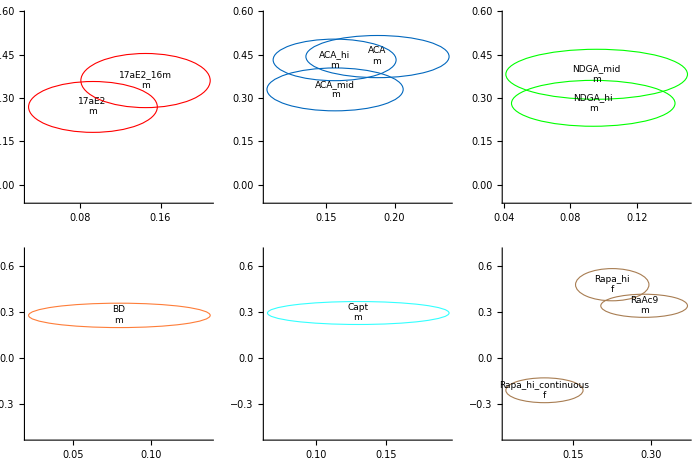

```mathematica
highlightedInds =Transpose[ Position[(Join@@relative)[[;;,2]],#][[1]]&/@Select[plotData,(#[[2,1]]&&#[[2,2]]&&#[[2,4]]!="8")&][[;;,2,{3,5,6}]]][[1]];
(*yEbarPlotData={Callout[Exp@{Around[#[[1]],14.1*#[[2]]]&@(Join@@relative)[[#,1,1]],Around[#[[1]],14.1*#[[2]]]&@(Join@@relative)[[#,1,2]]},plotData[[#,2,3]]],plotData[[#,3]]}&/@highlightedInds;
ListLogLogPlot[{#}&/@yEbarPlotData[[;;,1]],
PlotStyle->yEbarPlotData[[;;,2,2]],
(*PlotLegends->catLegend,*)
Frame->True,AspectRatio->1,Axes->True,AxesOrigin->{1,1},PlotRange->{{0.93,1.36},{0.65, 1.73}},ImageSize->560,FrameLabel->{"Relative Longevity","Relative Steepness"},FrameStyle->Directive[20,Black]]*)
GraphicsGrid[Table[
(#&/@(Graphics[#,AspectRatio->1,ImageSize->300,
AxesStyle->Directive[ Thick,Black],Frame->False,
PlotRange->{Automatic,{Log@{.95,1.8},Log@{.6,2.}}[[rng[[3]]/3]]}(*{Log@{1.05,1.45},Log@{.6,2.}}*),
(*FrameLabel->{"Longevity (years)","Steepness"},*)FrameStyle->Directive[Black,14],Axes->True,AxesOrigin->{0.,0.}
]&/@((Jdata[[#]]/.x:{{{{_Real,_Real}..},{{_Real,_Real}..}},_}:>{
FaceForm[],EdgeForm[plotData[[#,3,2]]],Ellipsoid@@(VectorAround[Mean@Log@x[[1,2]]-Mean@Log@x[[1,1]],Covariance@Log@x[[1,1]]+Covariance@Log@x[[1,2]]]),
Text[Style[StringJoin@Riffle[x[[2,2;;3]],"\n"],9],Mean@Log@x[[1,2]]-Mean@Log@x[[1,1]]]
}&/@GatherBy[highlightedInds,plotData[[#,2,4]]&][[rng]]
))
)),{rng,{{1,2,3},{4,5,6}}}],ImageSize->700]
```

```mathematica
Export[Basedir<>"NIA all stats iCV.csv",
Prepend[SortBy[Join@@{{#[[3]],#[[2]],#[[4]]},
{#[[3]],#[[2]],#[[4]]}/.(#[[2]]->#[[1]]&/@Join@@relative),
{{#[[3]],#[[2]],#[[4]]}/.(#[[2]][[{2,3,1}]]->#[[1]]&/@sortedPvalues),
#[[7]],#[[6]]}}&/@Import[Basedir<>"AFT+KS test results.csv"][[2;;]],{#[[1]],#[[2]]}&],
{"Label", "Gender", "Publication", "Relative longevity (Ln)", "Relative steepness (Ln)", "p-value", "KSm test stat", "KSm p-value"}
]
]
```

/Users/yifan/Library/CloudStorage/Dropbox/Current Projects/2023-AlonLab-sickspans/NIA figure/NIA all stats iCV.csv